## Testing bugs

### 1. Soliton density profile with ChplUltra Units leapfrog with ChplUltra units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc {rho0, rc} = {27492.260803351877, 0.05359134269304645}

#### import coordinates

```mathematica
bp7pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",1;;10,6;;7}];
bp7pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",11;;20,6;;7}];
bp7pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",101;;110,6;;7}];
bp7pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",201;;210,6;;7}];
bp7pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",301;;310,6;;7}];
bp7pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",991;;1000,6;;7}];
bp7pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",1991;;2000,6;;7}];
bp7pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",2991;;3000,6;;7}];
bp7pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",3991;;4000,6;;7}];
bp7pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",4991;;5000,6;;7}];
bp7pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",5991;;6000,6;;7}];
bp7pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",6991;;7000,6;;7}];
bp7pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",7991;;8000,6;;7}];
bp7pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",8991;;9000,6;;7}];
bp7pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",9991;;10000,6;;7}];
(*bp7pos1500= Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",14990;;15000,6;;7}];
bp7pos2000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",19990;;20000,6;;7}];
bp7pos3000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",29990;;30000,6;;7}]; *)
```

#### position

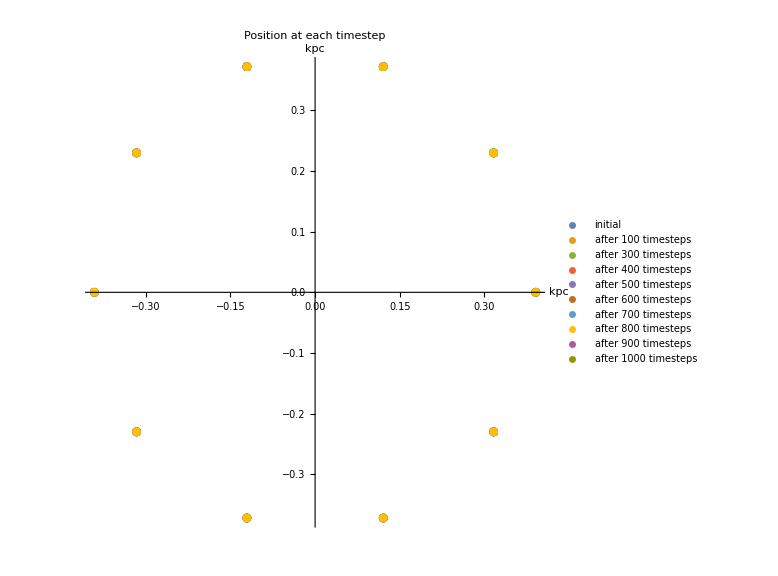

```mathematica
bp7posgraph = ListPlot[{bp7pos1,bp7pos10,bp7pos100,bp7pos300,bp7pos400,bp7pos500,bp7pos600,bp7pos700,bp7pos1500,bp7pos2000,bp7pos3000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

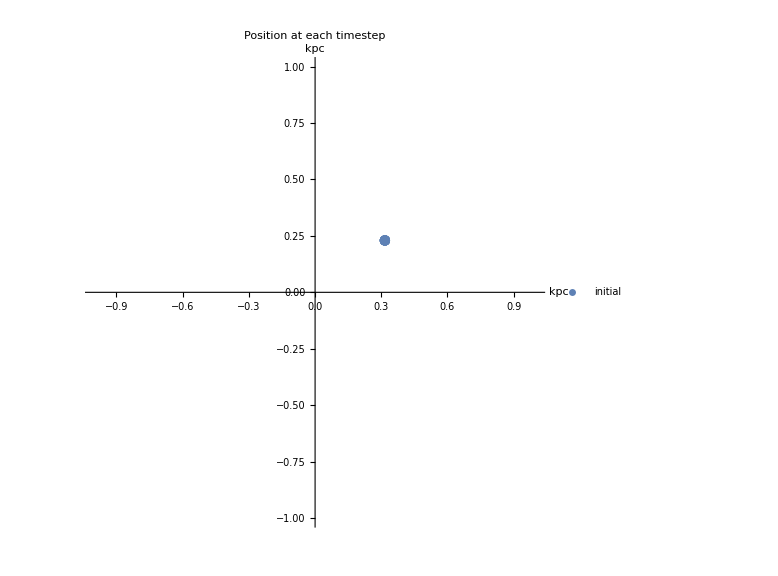

```mathematica
bp7posgraph = ListPlot[{bp7pos[[1]],bp7pos2[[1]],bp7pos100[[1]],bp7pos200[[1]],bp7pos300[[1]],bp7pos400[[1]],bp7pos500[[1]],bp7pos600[[1]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

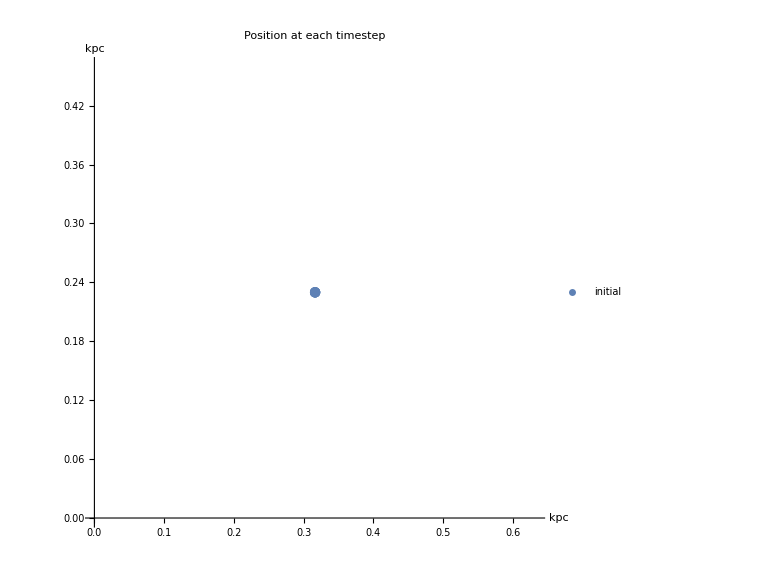

```mathematica
bp7posgraph = ListPlot[{bp7pos1[[1]],bp7pos2[[1]],bp7pos10[[1]],bp7pos30[[1]],bp7pos100[[1]]},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### 2. Soliton density profile with ChplUltra Units leapfrog with ChplUltra units 1 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc {rho0, rc} = {27492.260803351877, 0.05359134269304645}

#### Import Coordinates

```mathematica
bp8pos = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp8.csv",{"Data",1;;1002,6;;7}];
```

#### Position

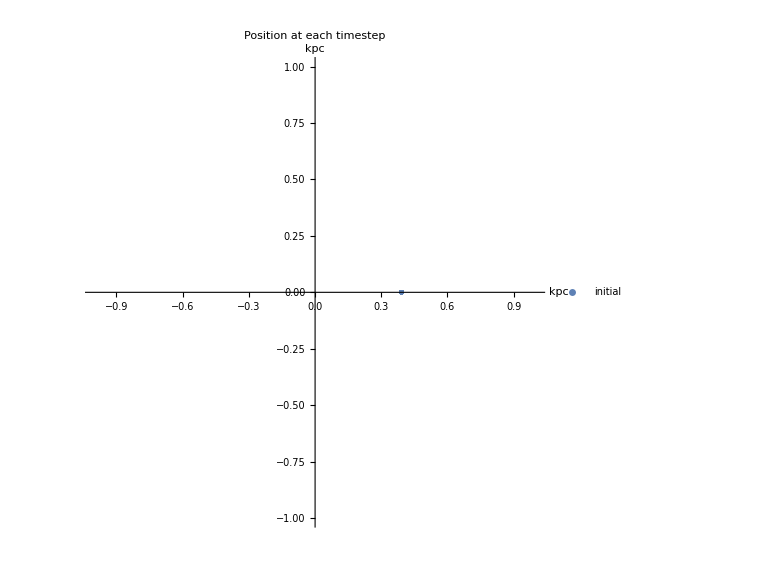

```mathematica
bp8posgraph = ListPlot[{bp8pos},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### 3. Box potential with ChplUltra Units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 1 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc, leapfrog box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp9pos = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp9.csv",{"Data",1;;1002,6;;7}];
```

#### Position

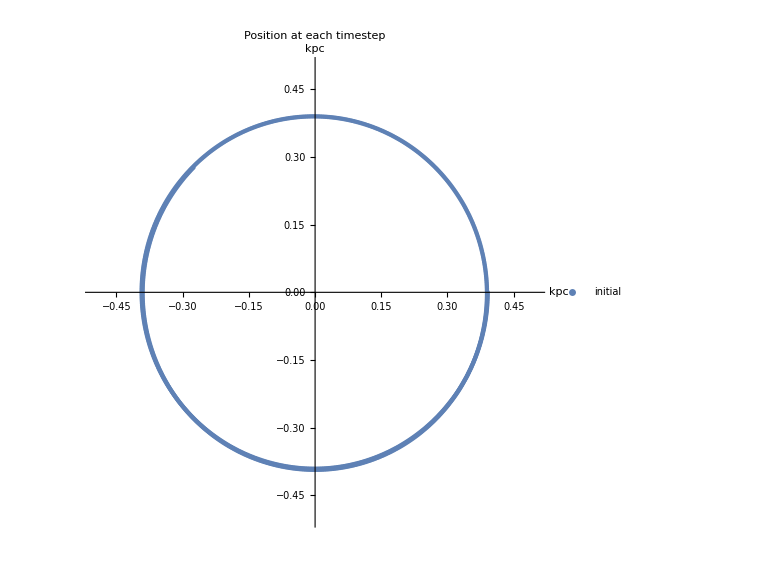

```mathematica
bp9posgraph = ListPlot[{bp9pos},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

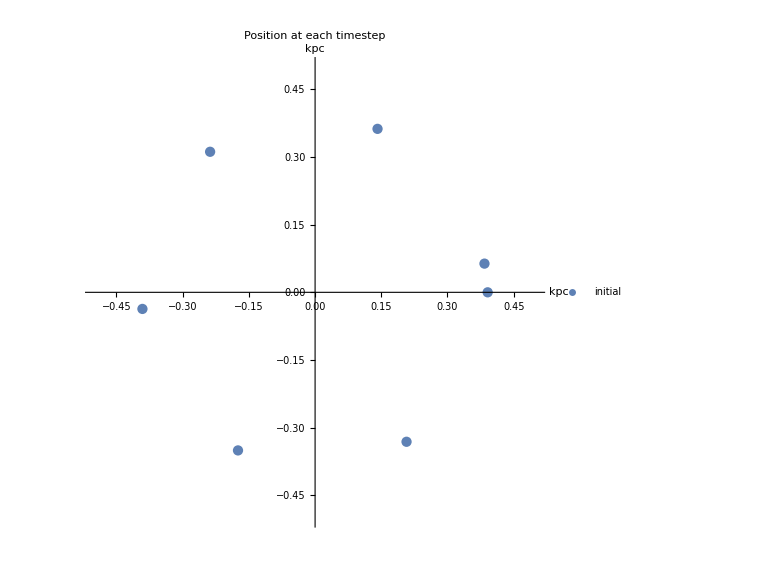

```mathematica
bp9posgraph = ListPlot[{bp9pos[[1]],bp9pos[[100]],bp9pos[[200]],bp9pos[[300]],bp9pos[[400]],bp9pos[[500]],bp9pos[[600]]},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### 4. Box potential with dimensionless units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 1 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc, leapfrog box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp10pos = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp10.csv",{"Data",1;;1002,6;;7}];
```

#### Position

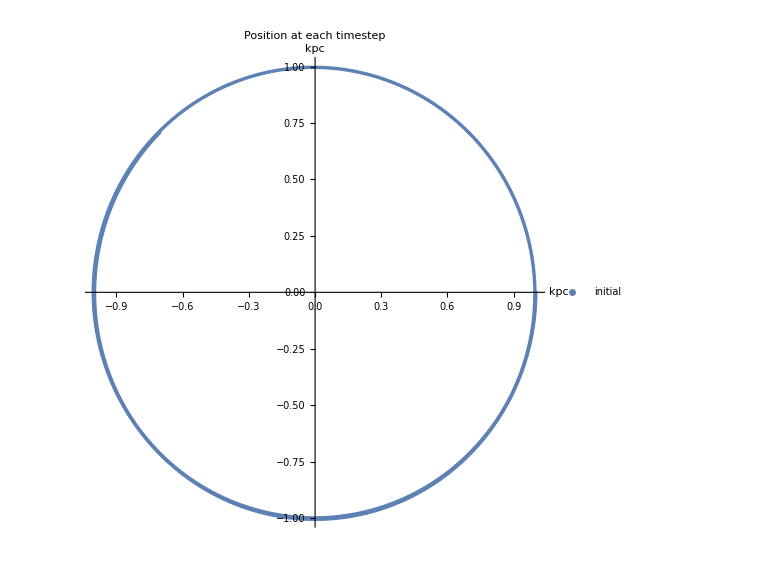

```mathematica
bp10posgraph = ListPlot[{bp10pos},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

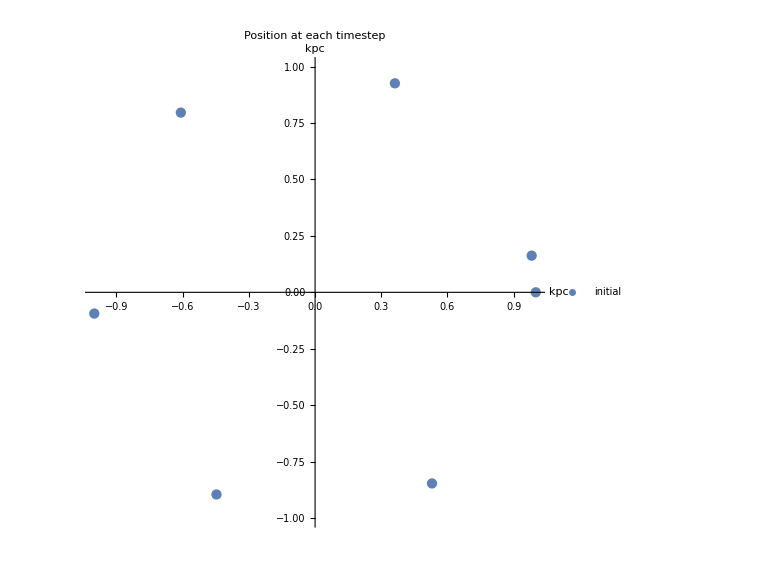

```mathematica
bp10posgraph = ListPlot[{bp10pos[[1]],bp10pos[[100]],bp10pos[[200]],bp10pos[[300]],bp10pos[[400]],bp10pos[[500]],bp10pos[[600]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### 5. Box potential with dimensionless units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc, leapfrog box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp11pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",1;;10,6;;7}];
bp11pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",11;;20,6;;7}];
bp11pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",91;;100,6;;7}];
bp11pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",191;;200,6;;7}];
bp11pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",291;;300,6;;7}];
bp11pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",991;;1000,6;;7}];
bp11pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",1991;;2000,6;;7}];
bp11pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",2991;;3000,6;;7}];
bp11pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",3991;;4000,6;;7}];
bp11pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",4991;;5000,6;;7}];
bp11pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",5991;;6000,6;;7}];
bp11pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",6991;;7000,6;;7}];
bp11pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",7991;;8000,6;;7}];
bp11pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",8991;;9000,6;;7}];
bp11pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp11.csv",{"Data",9991;;10000,6;;7}];
```

#### Position

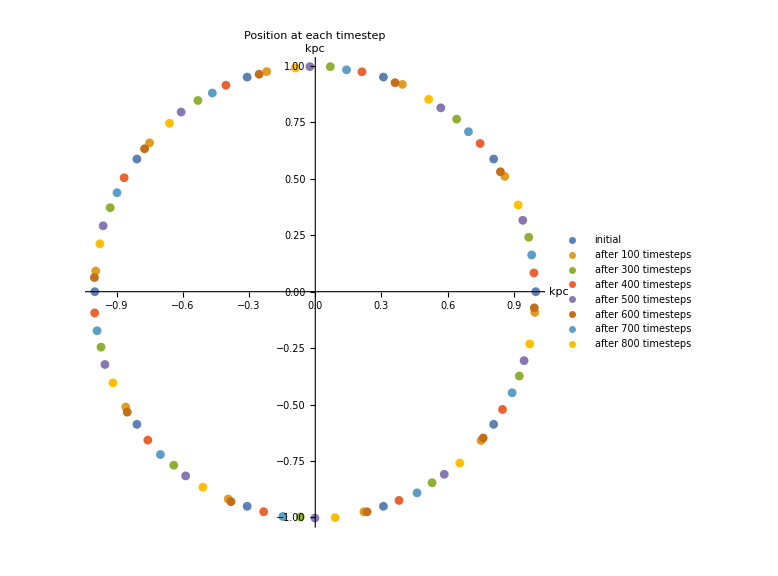

```mathematica
bp11posgraph = ListPlot[{bp11pos1,bp11pos10,bp11pos100,bp11pos300,bp11pos400,bp11pos500,bp11pos600,bp11pos700},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

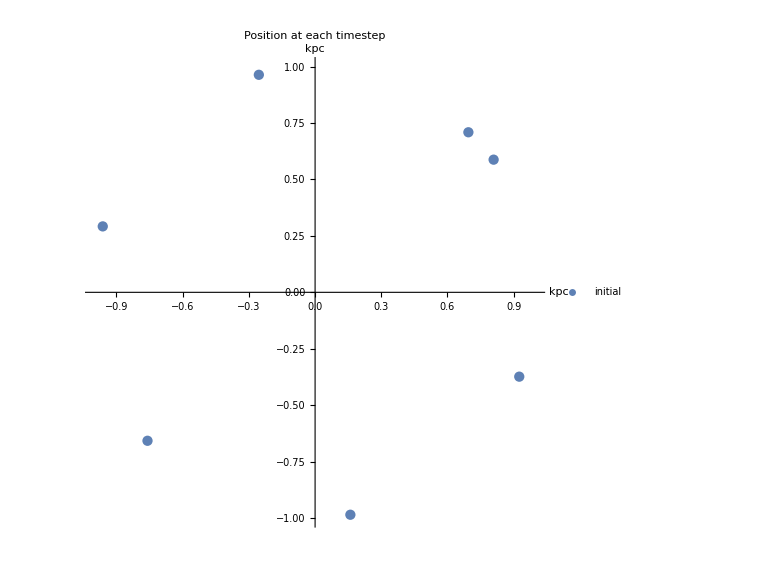

```mathematica
bp11posgraph = ListPlot[{bp11pos1[[1]],bp11pos100[[1]],bp11pos200[[1]],bp11pos300[[1]],bp11pos400[[1]],bp11pos500[[1]],bp11pos600[[1]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

```mathematica
(* period is back to 600+. Issue was in importing coordinates from 10-20: I was accidentally importing the coordinates of the last star of the previous timestep, and plotting those. *)
```

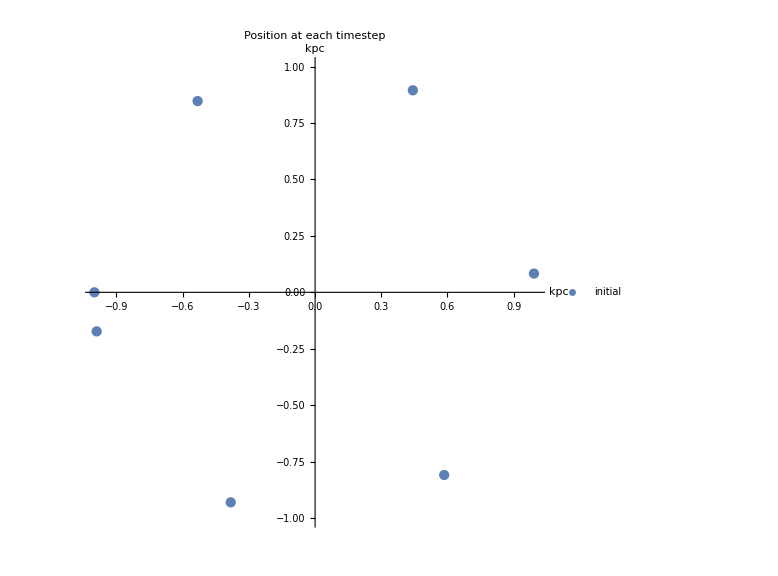

```mathematica
bp11pos22graph = ListPlot[{bp11pos1[[5]],bp11pos100[[5]],bp11pos200[[5]],bp11pos300[[5]],bp11pos400[[5]],bp11pos500[[5]],bp11pos600[[5]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### 6. Box potential with ChplUltra Units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc, leapfrog box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import coordinates

```mathematica
bp12pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",1;;10,6;;7}];
bp12pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",11;;20,6;;7}];
bp12pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",101;;110,6;;7}];
bp12pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",201;;210,6;;7}];
bp12pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",301;;310,6;;7}];
bp12pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",991;;1000,6;;7}];
bp12pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",1991;;2000,6;;7}];
bp12pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",2991;;3000,6;;7}];
bp12pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",3991;;4000,6;;7}];
bp12pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",4991;;5000,6;;7}];
bp12pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",5991;;6000,6;;7}];
bp12pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",6991;;7000,6;;7}];
bp12pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",7991;;8000,6;;7}];
bp12pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",8991;;9000,6;;7}];
bp12pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp12.csv",{"Data",9991;;10000,6;;7}];
```

#### Position

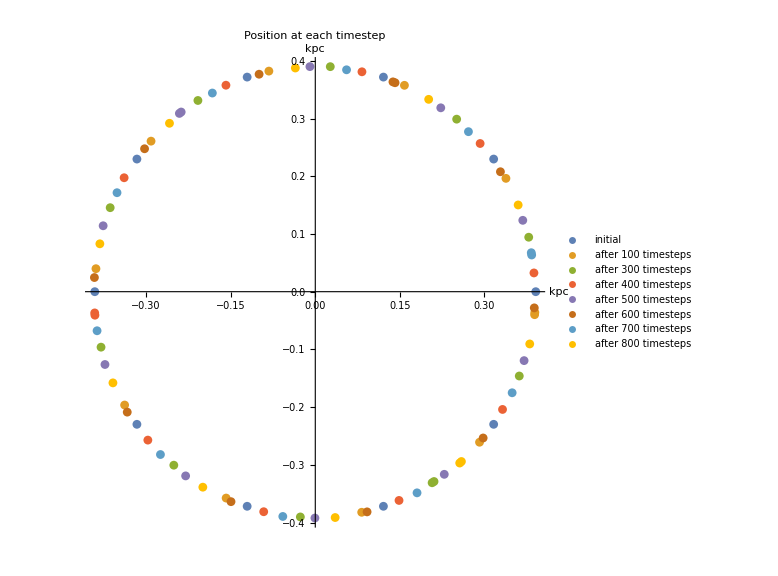

```mathematica
bp12posgraph = ListPlot[{bp12pos1,bp12pos10,bp12pos100,bp12pos300,bp12pos400,bp12pos500,bp12pos600,bp12pos700},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

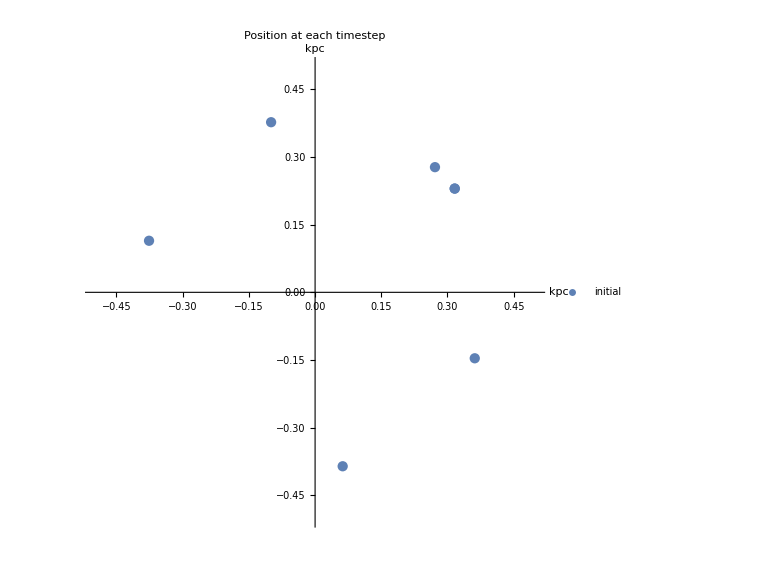

```mathematica
bp12posgraph = ListPlot[{bp12pos1[[1]],bp12pos100[[1]],bp12pos200[[1]],bp7pos300[[1]],bp12pos400[[1]],bp12pos500[[1]],bp12pos600[[1]]},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

## 7. Analytic NFW profile with dimensionless units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 1 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc, leapfrog

#### Import Coordinates

```mathematica
bp13pos = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp13.csv",{"Data",1;;1002,6;;7}];
```

#### Position

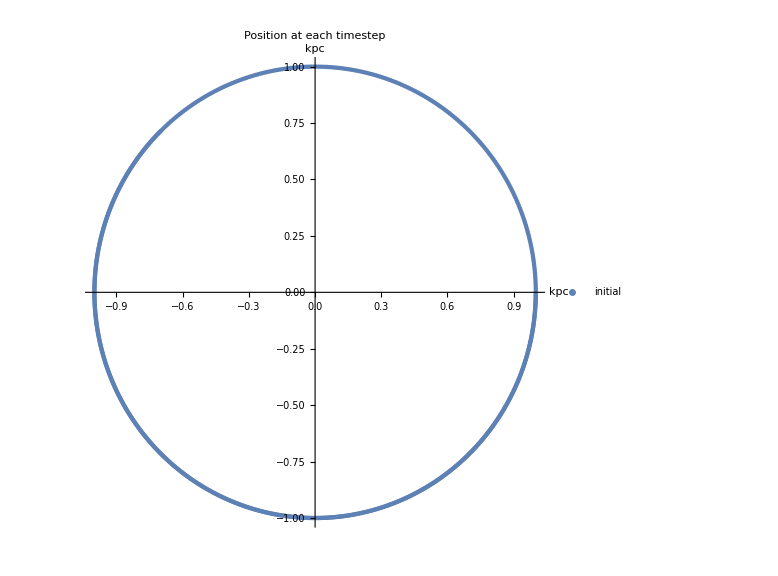

```mathematica
bp13posgraph = ListPlot[{bp13pos},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

```mathematica
bp10posgraph = ListPlot[{bp10pos[[1]],bp10pos[[100]],bp10pos[[200]],bp10pos[[300]],bp10pos[[400]],bp10pos[[500]],bp10pos[[600]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

-Graphics-

## 8. Analytic NFW profile with dimensionless units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc, leapfrog

#### Import Coordinates

```mathematica
bp14pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",1;;10,6;;7}];
bp14pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",11;;20,6;;7}];
bp14pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",101;;110,6;;7}];
bp14pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",201;;210,6;;7}];
bp14pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",301;;310,6;;7}];
bp14pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",991;;1000,6;;7}];
bp14pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",1991;;2000,6;;7}];
bp14pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",2991;;3000,6;;7}];
bp14pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",3991;;4000,6;;7}];
bp14pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",4991;;5000,6;;7}];
bp14pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",5991;;6000,6;;7}];
bp14pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",6991;;7000,6;;7}];
bp14pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",7991;;8000,6;;7}];
bp14pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",8991;;9000,6;;7}];
bp14pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp14.csv",{"Data",9991;;10000,6;;7}];
```

#### Position

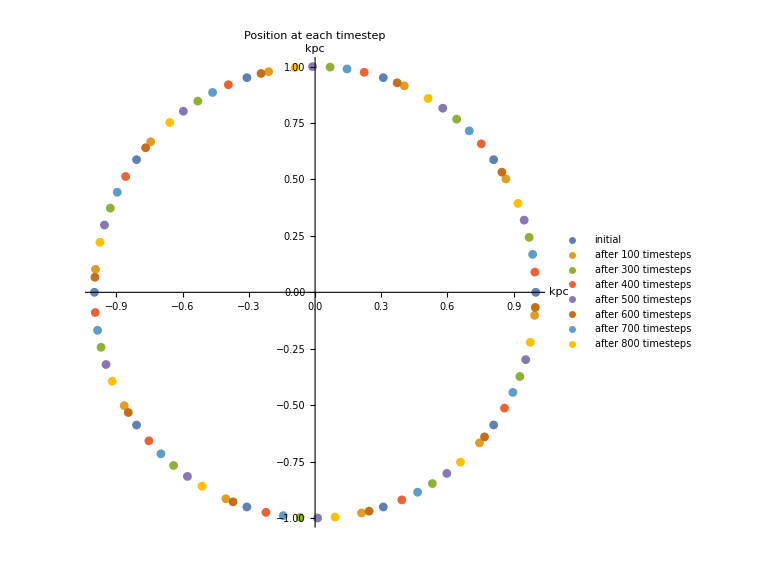

```mathematica
bp14posgraph = ListPlot[{bp14pos1,bp14pos10,bp14pos100,bp14pos300,bp14pos400,bp14pos500,bp14pos600,bp14pos700},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

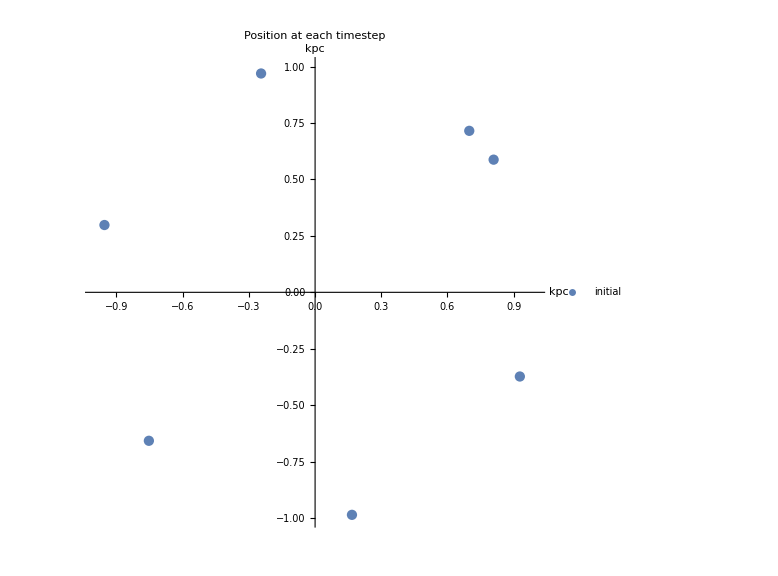

```mathematica
bp14posgraph = ListPlot[{bp14pos1[[1]],bp14pos100[[1]],bp14pos200[[1]],bp14pos300[[1]],bp14pos400[[1]],bp14pos500[[1]],bp14pos600[[1]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

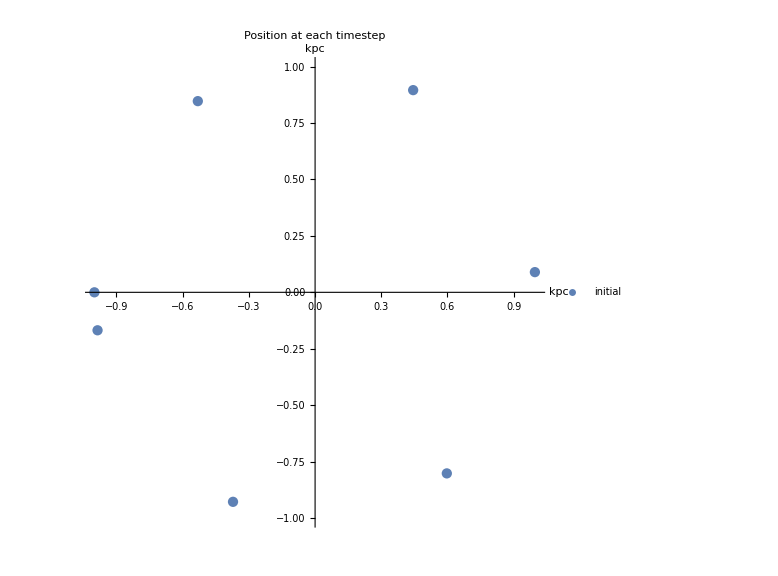

```mathematica
bp14posgraph = ListPlot[{bp14pos1[[5]],bp14pos100[[5]],bp14pos200[[5]],bp14pos300[[5]],bp14pos400[[5]],bp14pos500[[5]],bp14pos600[[5]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```